```mathematica
(*Load the Josh 2.0 library for every new *)
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
pos={0.09625,-78.0387}
(*At 70 --> 1.38012291979976*)
```

TEMPERATURE CONTROLLER CONTROLS

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]]
Needs["WolframMachineControl`"]
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
TempCtrlOff[]
```

0

```mathematica
TempCtrlInit[]
```

0

```mathematica
TempCtrlOn[]
```

0

```mathematica
TempCtrlPlotTemp[90,2]
```

TempCtrlPlotTemp[90,2]

```mathematica
TempCtrlSetSetpoint[90]
```

90.

```mathematica
TempCtrlGetTemp[]
```

76.19

BATH CONTROLS

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]]
Needs["WolframMachineControl`"]
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
BathOff[]
```

0

```mathematica
BathInit[]
```

0

```mathematica
BathOn[]
```

0

```mathematica
BathGetTemp[]
```

30.1

```mathematica
BathGetSetpoint[]
```

90.

```mathematica
BathSetSetpoint[30]
```

30.

SERVO CONTROLS

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]]
Needs["WolframMachineControl`"]
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
ServoDisable[]
```

0

```mathematica
ServoReady[]
```

0

```mathematica
ServoEnable[]
```

0

```mathematica
ServoHomed[]
```

ServoHomed[]

```mathematica
ServoHome[5000]
```

0

```mathematica
ServoGetPos[]
```

{0.09625,-78.0387}

```mathematica
ServoManualControl[]
```

0

LABJACK CONTROLS

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]]
Needs["WolframMachineControl`"]
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
ReadLabjack[3]
```

0.157659

```mathematica
LabJackTempSweep[10,{60,80,100},"monopalmatin_3",0,2]
```

Recorded 243 readings over 517 s -- saved to C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_3_60_rise_10_to_80.csv

Recorded 289 readings over 615 s -- saved to C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_3_60_fall_80_to_10.csv

Recorded 532 readings over 1133 s -- saved to C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_3_60_rise_10_to_100.csv

Recorded 320 readings over 681 s -- saved to C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_3_60_fall_100_to_10.csv

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_3_60_rise_10_to_80.csv,C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_3_60_fall_80_to_10.csv,C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_3_60_rise_10_to_100.csv,C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_3_60_fall_100_to_10.csv}

```mathematica
LabJackListCSVs[]
```

File Name | Date Created
monopalmatin_3_60_fall_100_to_10.csv | 2026-07-23  14:23:17
monopalmatin_3_60_rise_10_to_100.csv | 2026-07-23  14:11:56
monopalmatin_3_60_fall_80_to_10.csv | 2026-07-23  13:53:03
monopalmatin_3_60_rise_10_to_80.csv | 2026-07-23  13:42:47
monopalmatin_2_60_fall_100_to_10.csv | 2026-07-23  11:00:12
monopalmatin_2_60_fall_80_to_10.csv | 2026-07-23  10:33:36
monopalmatin_2_60_rise_10_to_80.csv | 2026-07-23  10:23:38
monopalmatin_2_60_rise_10_to_100.csv | 2026-07-23  10:03:59
monopalmatin_2_60_fall_60_to_10.csv | 2026-07-23  09:47:29
monopalmatin_2_60_rise_10_to_60.csv | 2026-07-23  09:38:56
monopalmatin_60_fall_100_to_10.csv | 2026-07-22  17:05:07
monopalmatin_60_rise_10_to_100.csv | 2026-07-22  16:53:55
monopalmatin_60_fall_80_to_10.csv | 2026-07-22  16:39:35
monopalmatin_60_rise_10_to_80.csv | 2026-07-22  16:29:41
monopalmatin_60_fall_60_to_10.csv | 2026-07-22  16:21:07
monopalmatin_60_rise_10_to_60.csv | 2026-07-22  16:12:36
monopalmatin_80_fall_85_to_10.csv | 2026-07-22  15:35:04
monopalmatin_80_rise_10_to_85.csv | 2026-07-22  15:24:40
monopalmatin_80_fall_75_to_10.csv | 2026-07-22  15:15:09
monopalmatin_80_rise_10_to_75.csv | 2026-07-22  15:05:34
monopalmatin_80_fall_65_to_10.csv | 2026-07-22  14:57:52
monopalmatin_80_rise_10_to_65.csv | 2026-07-22  14:48:55
monopalmatin_80_fall_55_to_10.csv | 2026-07-22  14:43:08
monopalmatin_80_rise_10_to_55.csv | 2026-07-22  14:35:13
monopalmatin_80_fall_45_to_10.csv | 2026-07-22  14:30:59
monopalmatin_80_rise_10_to_45.csv | 2026-07-22  14:23:59
monopalmatin_80_2.csv | 2026-07-22  13:54:29
monopalmatin_80.csv | 2026-07-22  13:30:53
monopalmatin_excess_2.csv | 2026-07-22  12:31:41
monopalmatin_excess.csv | 2026-07-22  12:10:06

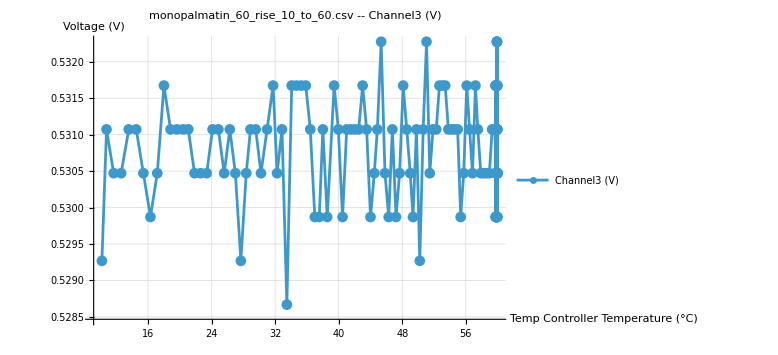

```mathematica
LabJackPlotData["monopalmatin_60_rise_10_to_60.csv",3]
```

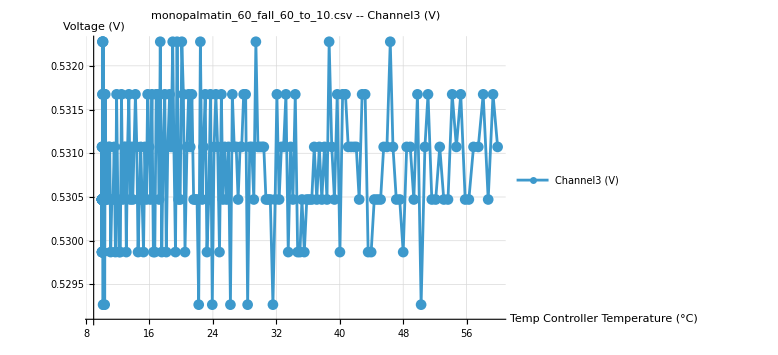

```mathematica
LabJackPlotData["monopalmatin_60_fall_60_to_10.csv",3]
```

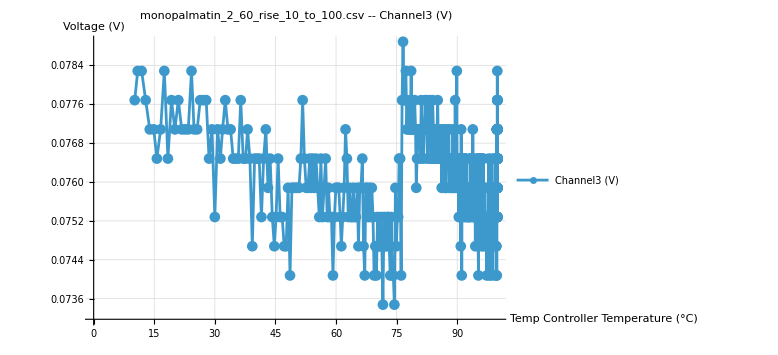

```mathematica
LabJackPlotData["monopalmatin_2_60_rise_10_to_100.csv",3]
```

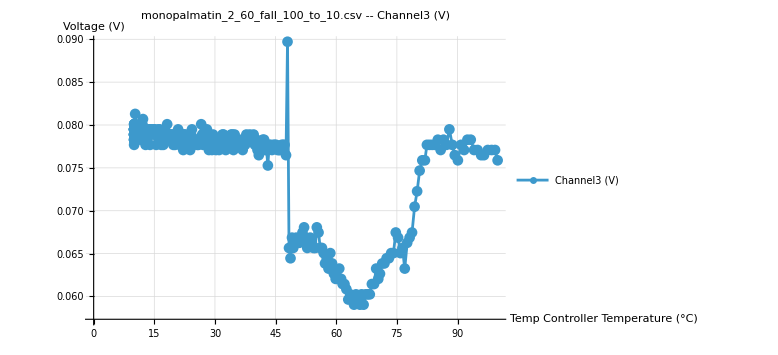

```mathematica
LabJackPlotData["monopalmatin_2_60_fall_100_to_10.csv",3]
```

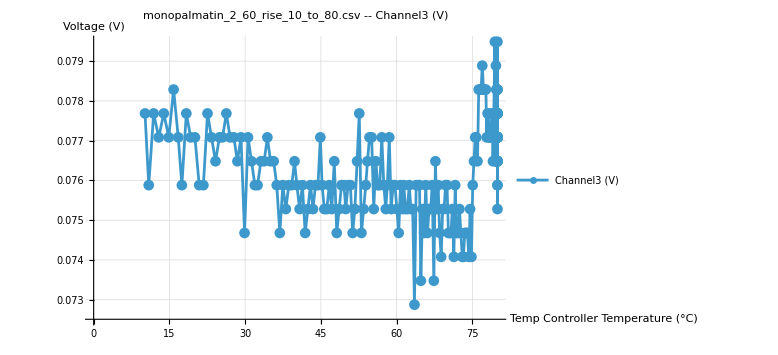

```mathematica
LabJackPlotData["monopalmatin_2_60_rise_10_to_80.csv",3]
```

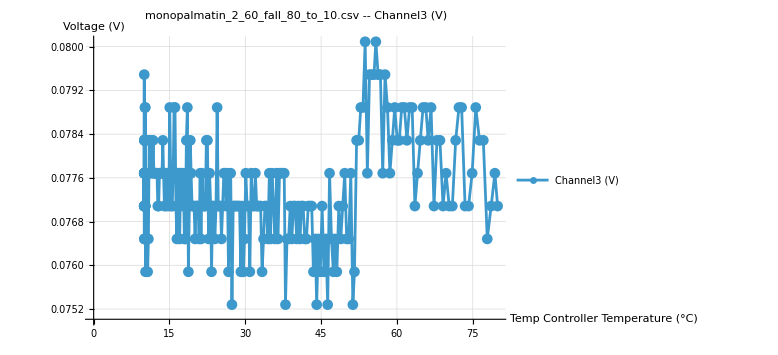

```mathematica
LabJackPlotData["monopalmatin_2_60_fall_80_to_10.csv",3]
```

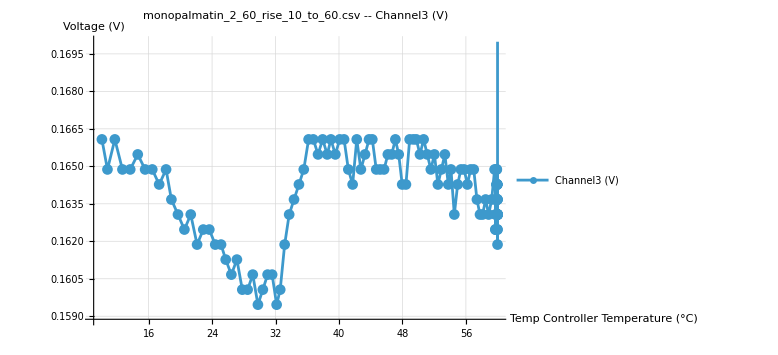

```mathematica
LabJackPlotData["monopalmatin_2_60_rise_10_to_60.csv",3]
```

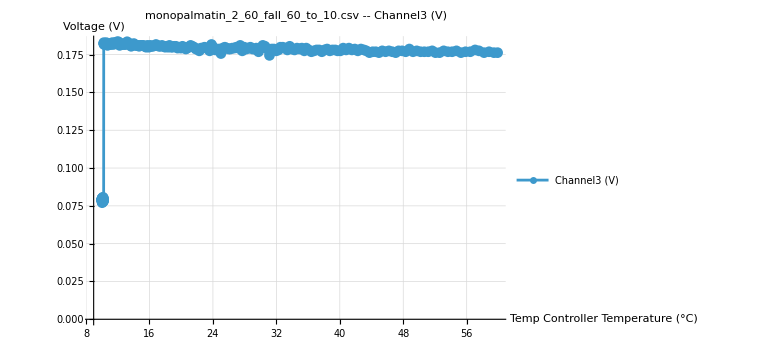

```mathematica
LabJackPlotData["monopalmatin_2_60_fall_60_to_10.csv",3]
```

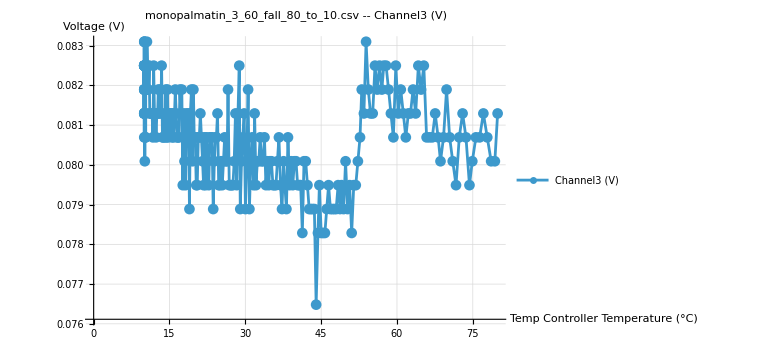

```mathematica
LabJackPlotData["monopalmatin_3_60_fall_80_to_10.csv",3]
```

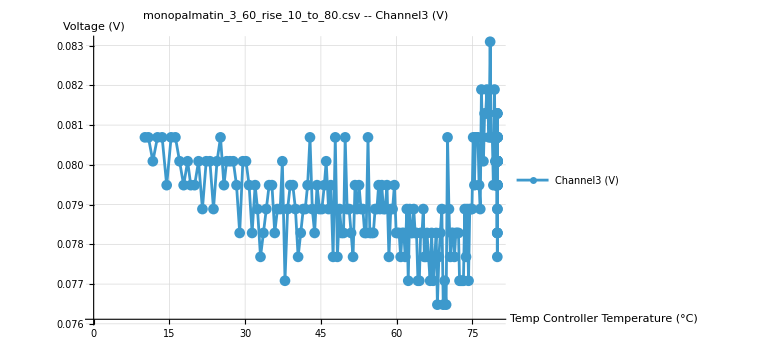

```mathematica
LabJackPlotData["monopalmatin_3_60_rise_10_to_80.csv",3]
```

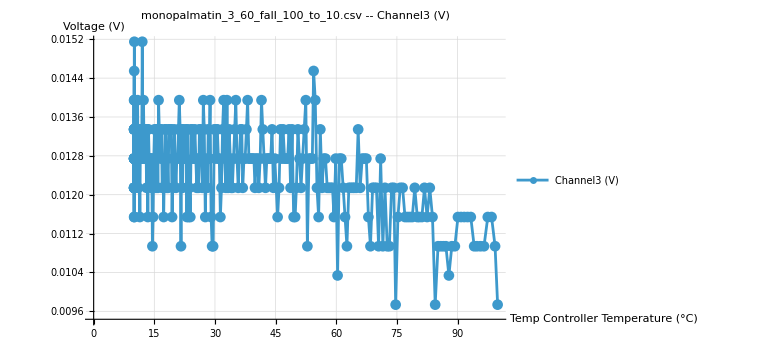

```mathematica
LabJackPlotData["monopalmatin_3_60_fall_100_to_10.csv",3]
```

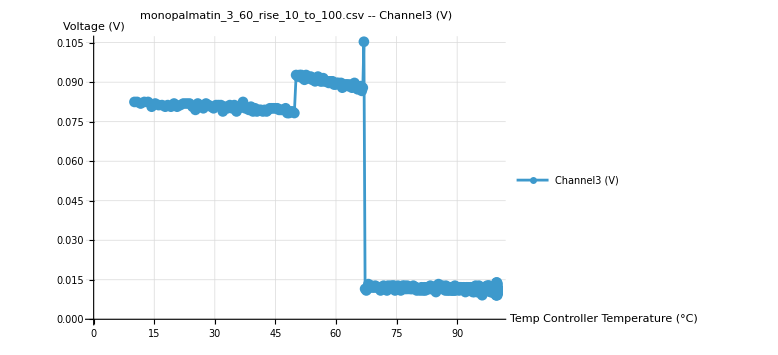

```mathematica
LabJackPlotData["monopalmatin_3_60_rise_10_to_100.csv",3]
```